```mathematica
Get["~/src/CelleratorML/1.0.3/CelleratorML.m"];
```

CelleratorML 1.0.3 (3 December 2008) loaded 03 December 2008 at 18:56 GMT-07:60 using Mathematica Version 7.0 for Linux x86 (32-bit) (November 11, 2008) Release 0; xlr8r 0.70; cellzilla 1.3.0; MathSBML 2.9.0; mPower 1.0.

#### AM Model 6 from SME

```mathematica
vars=List[r1,r2,r3,r4,r5,r6,r7,r8,r9,r10,r11,r12,r13];
reactionRates=List[Rule[r1,1.0000000000],Rule[r2,0.1000000000],Rule[r3,0.1000000000],Rule[r4,1.0000000000],Rule[r5,0.5000000000],Rule[r6,1.0000000000],Rule[r7,1.0000000000],Rule[r8,0.0100000000],Rule[r9,1.0000000000],Rule[r10,1.0000000000],Rule[r11,1.0000000000],Rule[r12,1.0000000000],Rule[r13,1.0000000000]];
initialCondi=List[Rule[AuxIAAProtein,0.0100000000],Rule[AuxIAAmRNA,0],Rule[AuxinSCFTIR1,0.0100000000],Rule[AuxinSCFTIR1AuxIAA,0],Rule[Auxin,0.1000000000],Rule[SCFTIR1,0.3000000000],Rule[AuxIAAmod,0]];
cmodel=Union[List[List[ShortRightArrow[AuxIAAmRNA,∅],r1]],List[List[ShortRightArrow[AuxIAAmod,∅],r2]],List[List[ShortRightArrow[AuxIAAProtein,∅],r3]],List[List[ShortRightArrow[AuxIAAmRNA,List[AuxIAAmRNA,AuxIAAProtein]],r4]],List[List[ShortRightArrow[AuxinSCFTIR1AuxIAA,List[AuxinSCFTIR1,AuxIAAmod]],r5]],List[List[RightArrowLeftArrow[List[AuxIAAProtein,AuxinSCFTIR1],AuxinSCFTIR1AuxIAA],r6,r7]],List[List[RightArrowLeftArrow[List[Auxin,SCFTIR1],AuxinSCFTIR1],r8,r9]],List[List[RightArrowLeftArrow[Auxin,∅],r10,r11]],List[List[RightArrowLeftArrow[SCFTIR1,∅],r12,r13]]];
```

```mathematica
Print[reactionRates]
```

{r1→1.,r2→0.1,r3→0.1,r4→1.,r5→0.5,r6→1.,r7→1.,r8→0.01,r9→1.,r10→1.,r11→1.,r12→1.,r13→1.}

```mathematica
Print[initialCondi]
```

{AuxIAAProtein→0.01,AuxIAAmRNA→0,AuxinSCFTIR1→0.01,AuxinSCFTIR1AuxIAA→0,Auxin→0.1,SCFTIR1→0.3,AuxIAAmod→0}

```mathematica
Print[cmodel]
```

{{AuxIAAmod→∅,r2},{AuxIAAmRNA→∅,r1},{AuxIAAmRNA→{AuxIAAmRNA,AuxIAAProtein},r4},{AuxIAAProtein→∅,r3},{AuxinSCFTIR1AuxIAA→{AuxinSCFTIR1,AuxIAAmod},r5},{Auxin⇄∅,r10,r11},{SCFTIR1⇄∅,r12,r13},{{AuxIAAProtein,AuxinSCFTIR1}⇄AuxinSCFTIR1AuxIAA,r6,r7},{{Auxin,SCFTIR1}⇄AuxinSCFTIR1,r8,r9}}

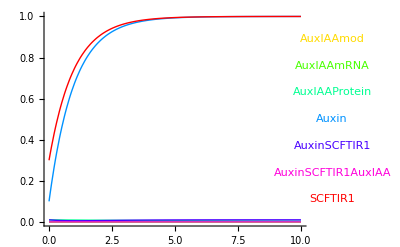

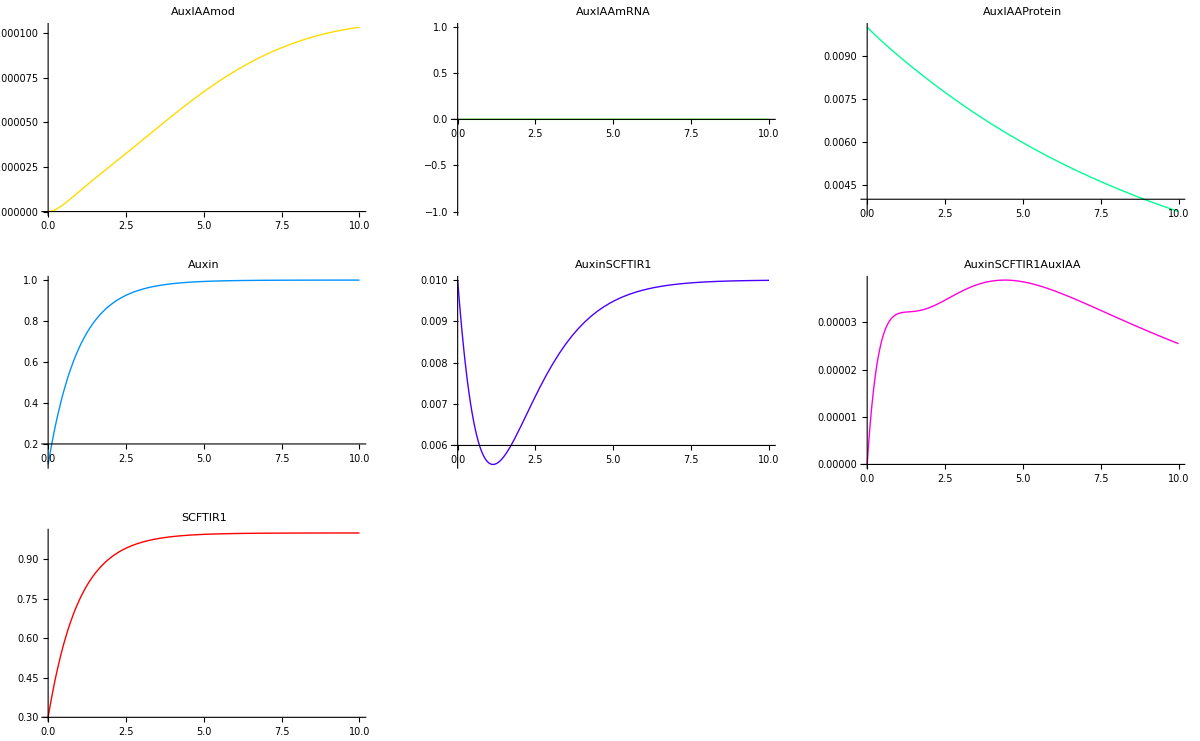

{{AuxIAAmod→InterpolatingFunction[{{0.,10.}},<>],AuxIAAmRNA→InterpolatingFunction[{{0.,10.}},<>],AuxIAAProtein→InterpolatingFunction[{{0.,10.}},<>],Auxin→InterpolatingFunction[{{0.,10.}},<>],AuxinSCFTIR1→InterpolatingFunction[{{0.,10.}},<>],AuxinSCFTIR1AuxIAA→InterpolatingFunction[{{0.,10.}},<>],SCFTIR1→InterpolatingFunction[{{0.,10.}},<>]}}

```mathematica
run[cmodel, initialConditions-> initialCondi, rates-> reactionRates, timeSpan-> 10, plot-> True, gridPlotVariables-> All]
```

#### Show basic help functions

```mathematica
?GetModel
```

GetModel[filename, options] returns {model, list-of-reation-rates, list-of-initial-conditions, list-of-options}

list-of-options={"Name"→modelname, "Frozen"→list-of-frozen-variables}

(Changed in 1.0.2 to include list-of-options)

Options are: 
"Quiet"→False, if True, will reduce the amount of printed output.

```mathematica
?SaveModel
```

SaveModel[model, options] writes a Cellerator model into xml text to screen
SaveModel[filename, model, options] writes xml to specified file; If the file already exists it is not overwritten, but a new file with a unique file name is created.

Options (note that all options are quoted strings, not symbols):

	"Name"→Optional model name
	"Parameters"→Optional list of parameters  (equivalent to SME reactionRates or run option rates)
	"InitialConditions"→Optional list of initail conditions (equivalent to SME initialCondi or run option initialConditions)
	"Frozen"→{}, List of Cellerator frozen varibles
	"Creator"→Optional textual annotation for creator's name; defaults to $UserName
	"email"→Optional creator's email
	"WebPage"→Optional creator's web page
	"Description"→Optional text or html description of model

Example:

SaveModel[{{A→B, k1}, {B→Q, k2}}, "Parameters"→{k1→1, k2→2}, "InitialConditions"→{A→5, B→7, Q→0}]

```mathematica
?LatexForm
```

LatexForm[model, rules, ic, outputfile.tex] generates a latex file describing the model.
LatexForm[model, rules, ic] autogenerates an output file name.
In each of these forms, model is a list of cellerator reactions; rules is a list of cellerator rate rules; and ic is a list of cellerator initial condition rules.

LatexForm[inputfile.xml, outputfile.tex] converts the CelleratorML file to latex.

LatexForm[inputfile.xml] autogenerates an output file name.

In any case if the specified output file already exists, a unique new file name is generated

The return value of LatexForm is always the name of the file created.

#### Save the model as CelleratorML

```mathematica
SaveModel["AM6.xml", cmodel,"Parameters"->reactionRates, "InitialConditions"-> initialCondi,   "Creator"-> "Joe The Plumber", "email"-> "joe@the.plumber.com", "WebPage"-> "http://www.joetheplumber.com", "Description"-> "CelleratorML file for Alastair Middleton's Auxin model, in SME, Version 6", "Name"-> "Middleton⎵Auxin⎵Model"]
```

AM6.xml

#### Read the CelleratorML and do a simulation

```mathematica
m=GetModel["AM6.xml", "Quiet"-> True]
```

{{{AuxIAAmod→∅,r2},{AuxIAAmRNA→∅,r1},{AuxIAAmRNA→{AuxIAAmRNA,AuxIAAProtein},r4},{AuxIAAProtein→∅,r3},{AuxinSCFTIR1AuxIAA→{AuxinSCFTIR1,AuxIAAmod},r5},{Auxin⇄∅,r10,r11},{SCFTIR1⇄∅,r12,r13},{{AuxIAAProtein,AuxinSCFTIR1}⇄AuxinSCFTIR1AuxIAA,r6,r7},{{Auxin,SCFTIR1}⇄AuxinSCFTIR1,r8,r9}},{r1→1.,r2→0.1,r3→0.1,r4→1.,r5→0.5,r6→1.,r7→1.,r8→0.01,r9→1.,r10→1.,r11→1.,r12→1.,r13→1.},{AuxIAAProtein→0.01,AuxIAAmRNA→0,AuxinSCFTIR1→0.01,AuxinSCFTIR1AuxIAA→0,Auxin→0.1,SCFTIR1→0.3,AuxIAAmod→0},{Name→Middleton⎵Auxin⎵Model,Frozen→{}}}

```mathematica
{net, rules, ic, opt}=m;
```

```mathematica
interpret[net]
```

{{AuxIAAmod'[t]==-r2 AuxIAAmod[t]+r5 AuxinSCFTIR1AuxIAA[t],AuxIAAmRNA'[t]==-r1 AuxIAAmRNA[t],AuxIAAProtein'[t]==r4 AuxIAAmRNA[t]-r3 AuxIAAProtein[t]-r6 AuxIAAProtein[t] AuxinSCFTIR1[t]+r7 AuxinSCFTIR1AuxIAA[t],Auxin'[t]==r11-r10 Auxin[t]+r9 AuxinSCFTIR1[t]-r8 Auxin[t] SCFTIR1[t],AuxinSCFTIR1'[t]==-r9 AuxinSCFTIR1[t]-r6 AuxIAAProtein[t] AuxinSCFTIR1[t]+r5 AuxinSCFTIR1AuxIAA[t]+r7 AuxinSCFTIR1AuxIAA[t]+r8 Auxin[t] SCFTIR1[t],AuxinSCFTIR1AuxIAA'[t]==r6 AuxIAAProtein[t] AuxinSCFTIR1[t]-r5 AuxinSCFTIR1AuxIAA[t]-r7 AuxinSCFTIR1AuxIAA[t],SCFTIR1'[t]==r13+r9 AuxinSCFTIR1[t]-r12 SCFTIR1[t]-r8 Auxin[t] SCFTIR1[t]},{AuxIAAmod,AuxIAAmRNA,AuxIAAProtein,Auxin,AuxinSCFTIR1,AuxinSCFTIR1AuxIAA,SCFTIR1}}

```mathematica
run[net, timeSpan-> 10, initialConditions-> ic, rates-> rules, gridPlotVariables-> All, plot-> True]
```

-Graphics-

-Graphics-

{{AuxIAAmod→InterpolatingFunction[{{0.,10.}},<>],AuxIAAmRNA→InterpolatingFunction[{{0.,10.}},<>],AuxIAAProtein→InterpolatingFunction[{{0.,10.}},<>],Auxin→InterpolatingFunction[{{0.,10.}},<>],AuxinSCFTIR1→InterpolatingFunction[{{0.,10.}},<>],AuxinSCFTIR1AuxIAA→InterpolatingFunction[{{0.,10.}},<>],SCFTIR1→InterpolatingFunction[{{0.,10.}},<>]}}

#### Convert to Latex

```mathematica
LatexForm["AM6.xml", "AM6.txt"]
```

AM6.txt

```mathematica
LatexForm[cmodel, reactionRates, initialCondi, "Another-AM6-Latex-Output.tex"]
```

Another-AM6-Latex-Output.tex